```mathematica
(*FUNCTION DEFINITION*)
(*SIGNAL ON*)
variables = {Bmax,Y0,Kd,x};
f=Function[Evaluate@variables,(Bmax-Y0)*x/(x+Kd)+Y0];

statsthreshold = 4.604;
xmin = -3;xmax =4;s=500;(*200*)
(*EXAMPLES:*)
	(*SIGNAL OFF*)
		(*variables = {Bmax,Y0,Kd,x};f=Function[Evaluate@variables,(Bmax-Y0)*Kd/(x+Kd)+Y0];*)
	(*LINEAR*)
		(*variables = {m,b,x};
		f=Function[Evaluate@variables,m*x+b];*)

numOfVars = Length[variables];
tab={Table[Subscript[c, i],{i,1,Length[variables]}]}//Flatten;
table=Table[(D[f @@tab,Subscript[c, i]]*Subscript[σ, Subscript[c, i]])^2,{i,1,numOfVars}]/.Table[tab[[i]]->variables[[i]],{i,numOfVars}];
sigmaf[X_]:=Sqrt[Sum[table[[i]],{i,1,numOfVars}]]/.{x->X}
ttest=Abs[(((f@@variables/.x->α x)-(f@@variables/.x-> x))/Sqrt[sigmaf[α x]^2+sigmaf[x]^2])/.Subscript[σ, α x]-> Subscript[σ, x]];

calculateResolution[values_,errors_,title_]:=
Module[{},{

substitution1=Table[Subscript[σ, variables[[i]]]->errors[[i]],{i,numOfVars}];
substitution2=Table[variables[[i]]->values[[i]],{i,numOfVars}];

sol=Solve[(ttest/.substitution1/.substitution2)==statsthreshold/Sqrt[3]&&α>1&&x>0,α];
(*sol=Solve[(ttest/.substitution1/.substitution2)==6.965/Sqrt[3]&&α>1&&x>0,α];*)

CI = 1.645;(*90% 1.645, 95% 1.960, 99% 2.576, 99.5% 2.807*)
Plot[{(f@@values)/.x->10^X,(f@@values+CI*sigmaf[x]/.substitution1/.substitution2)/.x->10^X,(f@@values-CI*sigmaf[x]/.substitution1/.substitution2)/.x->10^X,α/.sol/.x->10^X,2},{X,xmin,xmax},AxesOrigin->{xmin,0}],
fm=FindMinimum[α/.sol/.x->10^X,{X,Log10[values[[numOfVars-1]]]}],10^(X/.fm[[2]]),
alphas=Table[{(i-s*xmin+1),10^(i/s)//N,First[α/.sol/.x->10^(i/s)]},{i,s*xmin,s*xmax}];
undefPosition=First[Position [alphas,Undefined]//Flatten];
a1=alphas[[1;;undefPosition-1,2;;2]];
a2=alphas[[1;;undefPosition-1,3;;3]];
n2=Nearest[a2->a1,2,20]//Flatten;
Table[{First[Position [a1,n2[[i]]]//Flatten],n2[[i]]},{i,1,20}]//MatrixForm,
n5=Nearest[a2->a1,5,20]//Flatten;
Table[{First[Position [a1,n5[[i]]]//Flatten],n5[[i]]},{i,1,20}]//MatrixForm,
Export[title,alphas,"XLS"]
}];
(*fmlow=FindMinimum[Abs[2-α/.sol/.x->10^X],{X,-3+Log10[values[[numOfVars-1]]]}],ss=NSolve[{2== α/.sol/.x},{X,X/.fm[[2]]}],fmup=FindMinimum[Abs[2-α/.sol/.x->10^X],{X,Log10[values[[numOfVars-1]]]}],*)
```

Solve::ratnz: Solve was unable to solve the system with inexact coefficients. The answer was obtained by solving a corresponding exact system and numericizing the result.

FindMinimum::lstol: The line search decreased the step size to within the tolerance specified by AccuracyGoal and PrecisionGoal but was unable to find a sufficient decrease in the function. You may need more than MachinePrecision digits of working precision to meet these tolerances.

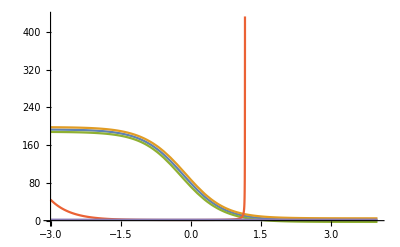
{-Graphics-,{1.43701,{X→-0.166718}},0.681211,(865 | 0.0534564
864 | 0.0532108
1891 | 6.0256
1892 | 6.05341
866 | 0.0537032
863 | 0.0529663
867 | 0.0539511
1890 | 5.99791
1893 | 6.08135
862 | 0.052723
868 | 0.0542001
861 | 0.0524807
1889 | 5.97035
1894 | 6.10942
869 | 0.0544503
860 | 0.0522396
870 | 0.0547016
1888 | 5.94292
859 | 0.0519996
1895 | 6.13762),(526 | 0.0112202
527 | 0.011272
2028 | 11.324
525 | 0.0111686
528 | 0.011324
524 | 0.0111173
529 | 0.0113763
523 | 0.0110662
2029 | 11.3763
530 | 0.0114288
522 | 0.0110154
531 | 0.0114815
2027 | 11.272
521 | 0.0109648
532 | 0.0115345
520 | 0.0109144
533 | 0.0115878
534 | 0.0116413
519 | 0.0108643
2030 | 11.4288),D_Proxim(revision).xls}

```mathematica
(*Assay D_Proxim (S1)*)
values={193.325640433207,1.12655914641329,0.693159083662151,x};errors={3.02855688021067,2.30652465748921,0.061338844702747,0};calculateResolution[values,errors,"D_Proxim(revision).xls"]
```

Solve::ratnz: Solve was unable to solve the system with inexact coefficients. The answer was obtained by solving a corresponding exact system and numericizing the result.

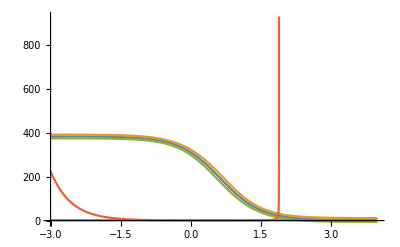
{-Graphics-,{1.50092,{X→0.533958}},3.41947,(1232 | 0.289734
2242 | 30.3389
1231 | 0.288403
1233 | 0.291072
2243 | 30.4789
2241 | 30.1995
1230 | 0.287078
1234 | 0.292415
2244 | 30.6196
1229 | 0.285759
1235 | 0.293765
2240 | 30.0608
1228 | 0.284446
1236 | 0.295121
2245 | 30.761
2239 | 29.9226
1227 | 0.283139
1237 | 0.296483
1226 | 0.281838
2246 | 30.903),(885 | 0.0586138
884 | 0.0583445
2391 | 60.256
886 | 0.0588844
883 | 0.0580764
887 | 0.0591562
882 | 0.0578096
888 | 0.0594292
2390 | 59.9791
881 | 0.057544
889 | 0.0597035
880 | 0.0572796
2392 | 60.5341
890 | 0.0599791
879 | 0.0570164
891 | 0.060256
878 | 0.0567545
892 | 0.0605341
2389 | 59.7035
877 | 0.0564937),E_Proxim(revision).xls}

```mathematica
(*Assay E_Proxim (S2/S3)*)
values={384.33493991299,2.67824855262922,4.289070622543,x};errors={5.01895587048414,5.23442554236231,0.436179912175753,0};calculateResolution[values,errors,"E_Proxim(revision).xls"]
```

Solve::ratnz: Solve was unable to solve the system with inexact coefficients. The answer was obtained by solving a corresponding exact system and numericizing the result.

FindMinimum::lstol: The line search decreased the step size to within the tolerance specified by AccuracyGoal and PrecisionGoal but was unable to find a sufficient decrease in the function. You may need more than MachinePrecision digits of working precision to meet these tolerances.

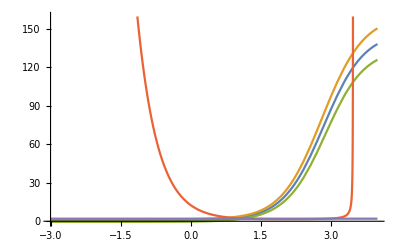
{-Graphics-,{1.648,{X→2.05909}},114.576,(2969 | 862.979
2105 | 16.1436
2106 | 16.2181
2970 | 866.962
2968 | 859.014
2104 | 16.0694
2107 | 16.293
2971 | 870.964
2103 | 15.9956
2967 | 855.067
2108 | 16.3682
2972 | 874.984
2102 | 15.9221
2109 | 16.4437
2966 | 851.138
2973 | 879.023
2101 | 15.8489
2110 | 16.5196
2965 | 847.227
2111 | 16.5959),(1739 | 2.99226
1738 | 2.97852
1740 | 3.00608
1737 | 2.96483
3173 | 2208.
3174 | 2218.2
1741 | 3.01995
1736 | 2.95121
1742 | 3.03389
1735 | 2.93765
1743 | 3.04789
1734 | 2.92415
3172 | 2197.86
1744 | 3.06196
3175 | 2228.44
1733 | 2.91072
1745 | 3.0761
1732 | 2.89734
1746 | 3.0903
1731 | 2.88403),F_QDirect(revision).xls}

```mathematica
(*Assay F - Qorvo (Direct)*)values={147.735236497151,0.481010101819776,704.074470831177,x};errors={7.91475045804365,0.598021661621242,77.7357123703907,0};calculateResolution[values,errors,"F_QDirect(revision).xls"]
```

Solve::ratnz: Solve was unable to solve the system with inexact coefficients. The answer was obtained by solving a corresponding exact system and numericizing the result.

FindMinimum::lstol: The line search decreased the step size to within the tolerance specified by AccuracyGoal and PrecisionGoal but was unable to find a sufficient decrease in the function. You may need more than MachinePrecision digits of working precision to meet these tolerances.

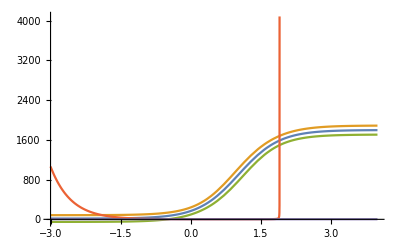
{-Graphics-,{1.89582,{X→0.824919}},6.6822,(1711 | 2.63027
2102 | 15.9221
1712 | 2.64241
2103 | 15.9956
1710 | 2.61818
2101 | 15.8489
1713 | 2.65461
2104 | 16.0694
1709 | 2.60615
2100 | 15.7761
1714 | 2.66686
2105 | 16.1436
1708 | 2.59418
1715 | 2.67917
2099 | 15.7036
2106 | 16.2181
1707 | 2.58226
1716 | 2.69153
2098 | 15.6315
1706 | 2.5704),(1232 | 0.289734
1231 | 0.288403
2385 | 58.6138
1233 | 0.291072
1230 | 0.287078
1234 | 0.292415
2384 | 58.3445
1229 | 0.285759
1235 | 0.293765
1228 | 0.284446
1236 | 0.295121
2386 | 58.8844
1227 | 0.283139
1237 | 0.296483
2383 | 58.0764
1238 | 0.297852
1226 | 0.281838
1239 | 0.299226
1225 | 0.280543
1240 | 0.300608),G_QEnzyme(revision).xls}

```mathematica
(*Assay G_Qorvo (Enzyme)*)values={1796.43776294984,8.16939188409543E-06,10.7477090570673,x};errors={55.2021021327212,41.1713554955947,1.65225707537587,0};calculateResolution[values,errors,"G_QEnzyme(revision).xls"]
```

Solve::ratnz: Solve was unable to solve the system with inexact coefficients. The answer was obtained by solving a corresponding exact system and numericizing the result.

FindMinimum::lstol: The line search decreased the step size to within the tolerance specified by AccuracyGoal and PrecisionGoal but was unable to find a sufficient decrease in the function. You may need more than MachinePrecision digits of working precision to meet these tolerances.

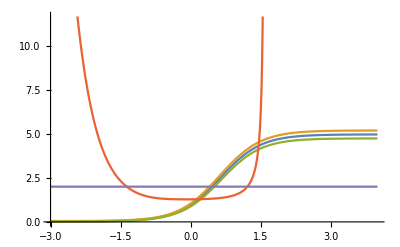
{-Graphics-,{1.27996,{X→-0.112402}},0.771966,(2108 | 16.3682
816 | 0.042658
817 | 0.0428549
2109 | 16.4437
815 | 0.042462
818 | 0.0430527
2107 | 16.293
814 | 0.0422669
819 | 0.0432514
2110 | 16.5196
2106 | 16.2181
820 | 0.043451
813 | 0.0420727
2111 | 16.5959
821 | 0.0436516
812 | 0.0418794
2105 | 16.1436
822 | 0.0438531
811 | 0.0416869
2112 | 16.6725),(503 | 0.0100925
2239 | 29.9226
504 | 0.0101391
502 | 0.0100462
505 | 0.0101859
501 | 0.01
506 | 0.0102329
500 | 0.00995405
2238 | 29.7852
507 | 0.0102802
499 | 0.00990832
508 | 0.0103276
2240 | 30.0608
498 | 0.00986279
509 | 0.0103753
497 | 0.00981748
510 | 0.0104232
496 | 0.00977237
511 | 0.0104713
2237 | 29.6483),A_Quantikine(revision).xls}

```mathematica
(*Assay A_Quantikine (CRP)*)values={4.96522217137017,0.0289917734723364,4.29896180778589,x};errors={0.136884468021632,0.0119964490676286,0.233369767021009,0};calculateResolution[values,errors,"A_Quantikine(revision).xls"]
```

Solve::ratnz: Solve was unable to solve the system with inexact coefficients. The answer was obtained by solving a corresponding exact system and numericizing the result.

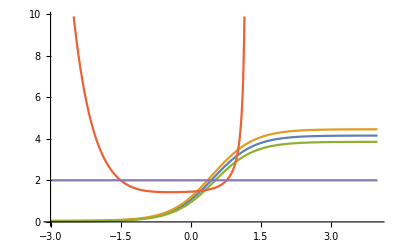
{-Graphics-,{1.42813,{X→-0.422844}},0.377708,(752 | 0.0317687
1886 | 5.88844
1887 | 5.91562
753 | 0.0319154
751 | 0.0316228
1885 | 5.86138
754 | 0.0320627
750 | 0.0314775
1888 | 5.94292
755 | 0.0322107
1884 | 5.83445
749 | 0.0313329
1889 | 5.97035
756 | 0.0323594
748 | 0.0311889
1883 | 5.80764
1890 | 5.99791
757 | 0.0325087
747 | 0.0310456
1882 | 5.78096),(424 | 0.00701455
425 | 0.00704693
2044 | 12.1899
423 | 0.00698232
426 | 0.00707946
422 | 0.00695024
427 | 0.00711214
2045 | 12.2462
421 | 0.00691831
428 | 0.00714496
420 | 0.00688652
429 | 0.00717794
2043 | 12.1339
419 | 0.00685488
430 | 0.00721107
431 | 0.00724436
418 | 0.00682339
2046 | 12.3027
432 | 0.0072778
417 | 0.00679204),B_Invitrogen(revision).xls}

```mathematica
(*Assay B_Invitrogen Human Instant ELISA Kit (CRP)*)values={4.15152272324893,0.0390860578241508,3.02796597536086,x};errors={0.183652871062456,0.00963118659185818,0.230254908551054,0};
calculateResolution[values,errors,"B_Invitrogen(revision).xls"]
```

Solve::ratnz: Solve was unable to solve the system with inexact coefficients. The answer was obtained by solving a corresponding exact system and numericizing the result.

FindMinimum::lstol: The line search decreased the step size to within the tolerance specified by AccuracyGoal and PrecisionGoal but was unable to find a sufficient decrease in the function. You may need more than MachinePrecision digits of working precision to meet these tolerances.

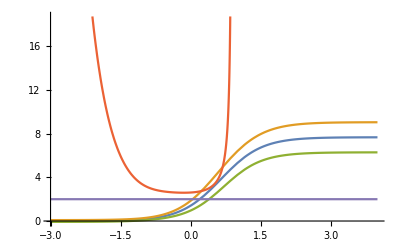
{-Graphics-,{2.5934,{X→-0.151055}},0.706228,(1425 | 0.704693
1426 | 0.707946
1424 | 0.701455
1427 | 0.711214
1423 | 0.698232
1428 | 0.714496
1422 | 0.695024
1429 | 0.717794
1421 | 0.691831
1430 | 0.721107
1420 | 0.688652
1431 | 0.724436
1419 | 0.685488
1432 | 0.72778
1418 | 0.682339
1433 | 0.731139
1417 | 0.679204
1434 | 0.734514
1416 | 0.676083
1435 | 0.737904),(808 | 0.041115
1845 | 4.87528
809 | 0.0413048
807 | 0.0409261
810 | 0.0414954
806 | 0.040738
1846 | 4.89779
1844 | 4.85289
811 | 0.0416869
805 | 0.0405509
812 | 0.0418794
804 | 0.0403645
1847 | 4.9204
813 | 0.0420727
1843 | 4.83059
803 | 0.0401791
814 | 0.0422669
802 | 0.0399945
815 | 0.042462
801 | 0.0398107),C_Invitrogen(revision).xls}

```mathematica
(*Assay C_Invitrogen Lot 1519925A*)values={7.67480558045665,1.10907559409696*10^-08,4.4505598273075,x};
errors={0.838934560582047,0.0499708290055094,0.85498007917499,0};calculateResolution[values,errors,"C_Invitrogen(revision).xls"]
```